```mathematica
c[k_,d_]:=k*d^2
```

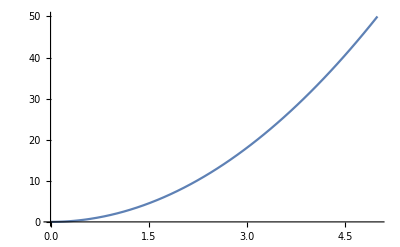

```mathematica
Plot[c[2,d],{d,0,5}, PlotRange->{0, Automatic}]
```

```mathematica
ξ[ϕ_,d_]:=Exp[-ϕ*d]
```

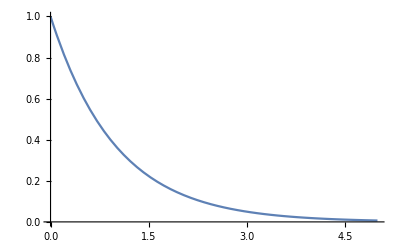

```mathematica
Plot[ξ[1,d],{d,0,5}, PlotRange->{0, 1}]
```

```mathematica
Exp[-2Log[2]]//N
```

0.25

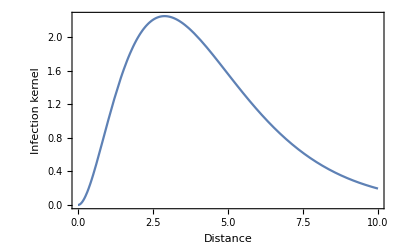

```mathematica
Plot[c[2,d]*ξ[Log[2],d],{d,0,10}, PlotRange->{0, Automatic}, Frame->{True,True,False,False},FrameLabel->{"Distance","Infection kernel"}]
```